```mathematica
FinancialData["IXC","Price"]
```

29.18 $

```mathematica
sAndp=FinancialData["IXC","Price",All]
```

TimeSeries[…]

```mathematica
Clear[sAndp]
```

```mathematica
FinancialData["INX","Price"]
```

0.34 C$

```mathematica
FinancialData["NDAQ","Price"]
```

100.13 $

```mathematica
FinancialData["IXIC","Price", All]
```

TimeSeries[…]

```mathematica
nasdaq=FinancialData["IXIC","Price", All]["Values"]
```

QuantityArray[…]

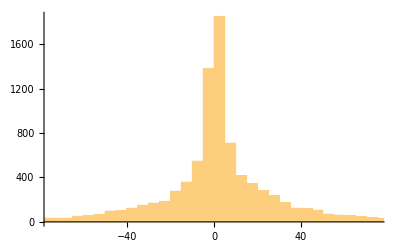

```mathematica
Histogram[Differences@nasdaq]
```

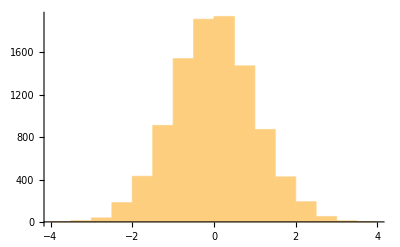

```mathematica
Histogram[RandomVariate[NormalDistribution[],10000]]
```

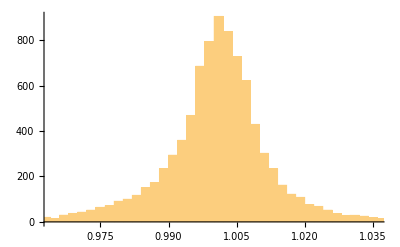

```mathematica
Histogram[Ratios@nasdaq]
```

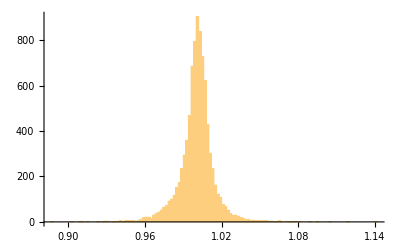

```mathematica
Histogram[Ratios@nasdaq,PlotRange->Full]
```

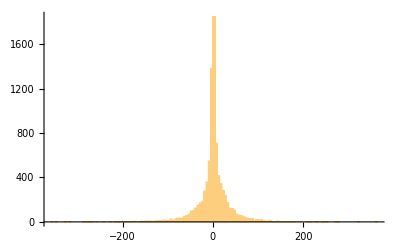

```mathematica
Histogram[Differences@nasdaq,PlotRange->Full]
```

```mathematica
FinancialData["IXIC","Price"]
```

7991.39

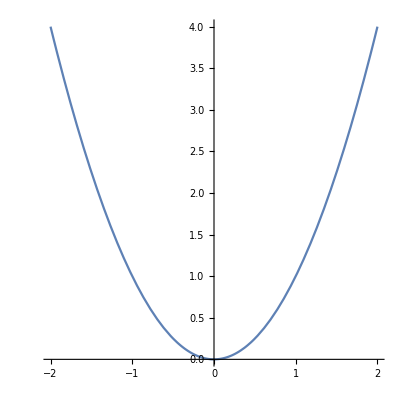

```mathematica
ParametricPlot[{t,t^2},{t,-2,2}]
```

```mathematica
PDF[NormalDistribution[],t]
```

(ⅇ^(-t^2/2))/(√(2 π))

```mathematica
D[{t,t^2},t]2 ⅇ^(-t^2/2)
```

{2 ⅇ^(-t^2/2),4 ⅇ^(-t^2/2) t}

```mathematica
Integrate[{2 ⅇ^(-t^2/2),4 ⅇ^(-t^2/2) t},t]
```

{√(2 π) Erf[t/(√2)],-4 ⅇ^(-t^2/2)}

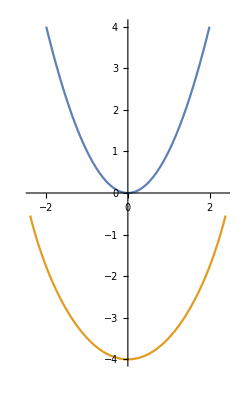

```mathematica
ParametricPlot[{
{t,t^2},{√(2 π) Erf[t/(√2)],-4 ⅇ^(-t^2/2)}
},{t,-2,2}]
```

```mathematica
FinancialData["DJI","Price"]
```

26252.2

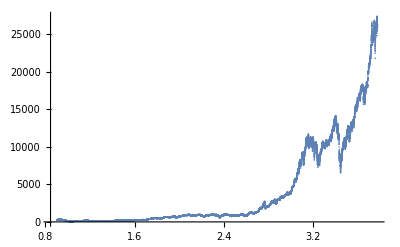

```mathematica
ListPlot[FinancialData["DJI","Price",All]]
```

```mathematica
Information@nasdaq
```

Information[QuantityArray[…]]

```mathematica
LinguisticAssistant
```